## Setup

```mathematica
Get["FunKit`"]
```

Loading external dependencies...

TensorBases loaded

MaTeX loaded

Loading modules...

...FEDeriK loaded

...AnSEL loaded

...DiANE loaded

...DiRK loaded

...TRACY loaded

...COEN loaded

...SeDecA loaded

Welcome to  █▀ ▐▄█ █▚▌ ▐◀ █ ▀█▀
Author: Franz Richard Sattler
Version: 1.0
Year: 2025
For more information, call FInfo[].

```mathematica
fields= <|
"cField"-> {A[p,{v, c}]},
"Grassmann"->{{cb[p,{c}],c[p,{c}]}}
|>;
truncation=<|
GammaN->{{A,A},{A,A,A},{A,A,A,A},{A,cb,c},{cb,c}},
Propagator->{{A,A},{cb,c}},Rdot->{{A,A},{cb,c}},
S->{{A,A},{A,A,A},{A,A,A,A},{cb,c},{cb,c,A}},
Field->{{}}
|>;
bases=<|
GammaN->{{A,A}->{"AA",1},{A,A,A}->"AAAClass",{A,A,A,A}->"AAAAClass",{A,cb,c}->{"Acbc",1},{cb,c}->"cbc"},
S->{{A,A}->{"AA",1},{A,A,A}->"AAAClass",{A,A,A,A}->"AAAAClass",{A,cb,c}->{"Acbc",1},{cb,c}->"cbc"},
Propagator->{{A,A}->"AA",{cb,c}->"cbc"},
Rdot->{{A,A}->{"AA",1},{cb,c}->"cbc"}
|>;
diagramStyling=<|
"Styles"->{A->{Orange},c->{Black,Dashed}}
|>;
Setup=<|
"FieldSpace"->fields,
"Truncation"->truncation,
"FeynmanRules"->bases,
"DiagramStyling"->diagramStyling
|>;

SetTexStyles[cb->"\\bar{c}"];
SetGlobalSetup[Setup];
dressingRules=ReplaceRepeated[#,{
dressing[GammaN,{A,A},2,{a_,b_}]:>1,
dressing[GammaN,{c,cb},1,{p1_,p2_}]:>ZA[√sp[p2,p2]]sp[p2,p2],
dressing[GammaN,{A,A},1,{p1_,p2_}]:>Zc[√sp[p2,p2]]sp[p2,p2],
dressing[GammaN,{c,cb,A},1,{p1_,p2_,p3_}]:>ZccbA[p1,p2], 
dressing[GammaN,{A,A,A},1,{p1_,p2_,p3_}]:>ZA3[p1,p2], 
dressing[GammaN,{A,A,A,A},1,{p1_,p2_,p3_,p4_}]:>ZA4[p1,p2,p3] ,

dressing[S,{c,cb,A},1,{p1_,p2_,p3_}]:>gS, 
dressing[S,{A,A,A},1,{p1_,p2_,p3_}]:>gS, 
dressing[S,{A,A,A,A},1,{p1_,p2_,p3_,p4_}]:>gS^2,

dressing[S,{c,cb},1,{p1_,p2_}]->sp[p2,p2],
dressing[S,{A,A},1,{p1_,p2_}]->sp[p2,p2],

ZccbA[p1_,p2_]:>ZccbA[√(1/3(sp[p1,p1]+sp[p2,p2]+sp[-p1-p2,-p1-p2]))],
ZA3[p1_,p2_]:>ZA3[√(1/3(sp[p1,p1]+sp[p2,p2]+sp[-p1-p2,-p1-p2]))],
ZA4[p1_,p2_,p3_]:>ZA4[√(1/4(sp[p1,p1]+sp[p2,p2]+sp[p3,p3]+sp[-p1-p2-p3,-p1-p2-p3]))],

nZA->6,
evP:>(k^nZA+1)^(1/nZA),
devP:>k^(-1+nZA) (1+k^nZA)^(-1+1/nZA),
dressing[Rdot,{A,A},1,{p1_,p2_}]:>ZA[evP]RBdot[k^2,sp[p2,p2]]+RB[k^2,sp[p2,p2]](dtZA[evP]+k*devP*((ZA[1.02evP]-ZA[evP])/(0.02*evP))),
dressing[Rdot,{c,cb},1,{p1_,p2_}]:>Zc[k]RBdot[k^2,sp[p2,p2]]+RB[k^2,sp[p2,p2]](dtZc[k]+k((Zc[1.02*k]-Zc[k])/(0.02*k)))
}]&;

SetSymmetricDressing[GammaN,{A,A}]
PropParam[expr_]:=UseLorentzLinearity[expr]//.{sp[p1,p1]->p^2,sp[l2,l2]->l2^2,sp[l1,l1]->l1^2,sp[l1,p1]->l1 p cos[p,l1],sp[l2,p1]->l2 p cos[p,l2],sp[l1,l2]->l1 l2 cos[l1,l2],√(a_^2):>a}//DiagramSimplify;
SPParam[expr_]:=UseLorentzLinearity[expr]//.{sp[p,p]->p^2,sp[l1,l1]->l1^2,sp[l1,l2]->l1 l2 cos[l1,l2],√(a_^2):>a}//DiagramSimplify;
SetNc[3]
$Assumptions=k>0&&p>0&&l1>0&&-1<cos1<1-1<cos2<1&&-1<cos3<1;
```

## DSE

## 2-Point

```mathematica
symmetryP2={Map[Join[#/.Cycles->Sequence,{1}]&,PermutationCycles/@Permutations[{1,2}]],{i1,i2}};
```


-Graphics-+-Graphics-/2--Graphics-/2--Graphics-/6--Graphics-+-Graphics-/2

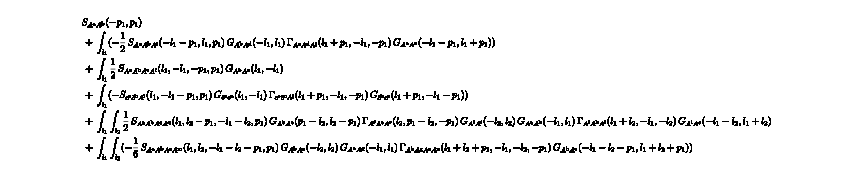

auto DSEAA1Loop(const auto &l1, const auto &p, const auto &cos, const auto &gS, const auto &ZA, const auto &Zc,
                const auto &ZA3, const auto &ZccbA)
{
  const auto _repl1 = cos(p, l1);
  const auto _repl2 = Zc(l1);
  const auto _repl3 = Zc(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p, l1)));
  return ((2. + powr<2>(_repl1) + powr<-2>(l1) * (7. + -1. * powr<2>(_repl1)) / (_repl2)) * gS +
          -0.5 * powr<-2>(l1) * ZA3(0.816496580927726 * sqrt(powr<2>(l1) + _repl1 * l1 * p + powr<2>(p))) *
              (-1. * (-1. + powr<2>(_repl1)) * powr<2>(l1) * powr<4>(p) +
               powr<2>(powr<2>(l1) + -1. * powr<2>(p)) * (2. + powr<2>(_repl1)) / (_repl2) +
               powr<2>(l1) * powr<2>(l1 + 2. * _repl1 * p) * powr<-1>(powr<2>(l1) + 2. * _repl1 * l1 * p + powr<2>(p)) *
                   (2. * powr<2>(l1) + powr<2>(_repl1) * powr<2>(l1) + 6. * _repl1 * l1 * p + 3. * powr<2>(p)) /
                   (_repl3) +
               -4. * powr<-1>(powr<2>(l1) + 2. * _repl1 * l1 * p + powr<2>(p)) *
                   (3. * powr<4>(l1) + 8. * powr<2>(l1) * powr<2>(p) + powr<2>(_repl1) * powr<2>(l1) * powr<2>(p) +
                    3. * powr<4>(p) + 6. * (powr<2>(l1) + powr<2>(p)) * _repl1 * l1 * p) /
                   (_repl3) * (-1. + powr<2>(_repl1)) / (_repl2)) /
              (powr<2>(l1) + 2. * _repl1 * l1 * p + powr<2>(p)) +
          powr<-1>(ZA(l1)) * powr<-1>(ZA(sqrt(powr<2>(l1) + 2. * _repl1 * l1 * p + powr<2>(p)))) *
              ZccbA(0.816496580927726 * sqrt(powr<2>(l1) + _repl1 * l1 * p + powr<2>(p))) * (-1. + powr<2>(_repl1)) /
              (powr<2>(l1) + 2. * _repl1 * l1 * p + powr<2>(p))) *
         gS;
}

```mathematica
DSEAA=TakeDerivatives[MakeDSE[Setup,A[i1]],{A[i2]}]//FTruncate//FSimplify[#,"Symmetries"->symmetryP2]&//FPlot//FRoute//FPrint;
DSEAAResult=Map[
(FormTrace[
F[TBGetProjector["AA",1,{i1,i2}/.#["ExternalIndices"]],#["Expression"]/.MakeDiagrammaticRules[]]
]//dressingRules//FORMSimplify//PropParam)&,
DSEAA]
MakeCppFunction[DSEAAResult["1-Loop"],"Name"->"DSEAA1Loop","Parameters"->{"l1","p","cos","gS","ZA","Zc","ZA3","ZccbA"}]
```

```mathematica
DSEcbc=TakeDerivatives[MakeDSE[Setup,c[i1]],{cb[i2]}]//FTruncate//FSimplify//FPlot//FRoute//FPrint;
DSEcbcResult=Map[
(FormTrace[
F[TBGetProjector["cbc",1,{i1,i2}/.#["ExternalIndices"]],#["Expression"]/.MakeDiagrammaticRules[]]
]//dressingRules//FORMSimplify//PropParam)&,
DSEcbc]
```

-Graphics-+-Graphics-

-Graphics-

<|0-Loop→p^2,1-Loop→(3 gS p^2 (-1+cos[p,l1]^2) ZccbA[√(2/3) √(l1^2+p^2+l1 p cos[p,l1])])/(l1^2 (l1^2+p^2+2 l1 p cos[p,l1]) ZA[√(l1^2+p^2+2 l1 p cos[p,l1])] Zc[l1])|>

## 3Point

```mathematica
symmetryP3={Map[Join[#/.Cycles->Sequence,{1}]&,PermutationCycles/@Permutations[{1,2,3}]],{i1,i2,i3}};
SP3FormRule=MakeSPFormRule[{l1},p,{p1,p2,p3}];
```

```mathematica
DSEAcbc=TakeDerivatives[MakeDSE[Setup,c[i1]],{A[i3],cb[i2]}]//FTruncate//FSimplify//FPlot//FRoute//FPrint;
DSEAcbcResult=Map[
(FormTrace[
F[TBGetProjector["Acbc",1,{i3,i2,i1}/.#["ExternalIndices"]],#["Expression"]/.MakeDiagrammaticRules[]]
,SP3FormRule,SP3FormRule]//dressingRules//(FORMSimplify[#,SP3FormRule,SP3FormRule]&)//SPParam)&,
DSEAcbc]
```

-Graphics---Graphics-+-Graphics-

-Graphics-

<|0-Loop→gS,1-Loop→1/(4 l1^2 Zc[l1])gS p (((3 p+2 l1 cos[p1,l1]-2 l1 cos[p2,l1]) (1+2 cos[p1,l1] cos[p2,l1]) ZccbA[√((2 l1^2)/3+p^2+2/3 l1 p (cos[p1,l1]-cos[p2,l1]))] ZccbA[√(2/3) √(l1^2+p^2-l1 p cos[p2,l1])])/((l1^2+p^2+2 l1 p cos[p1,l1]) (l1^2+p^2-2 l1 p cos[p2,l1]) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])] ZA[√(l1^2+p^2-2 l1 p cos[p2,l1])])+(2 (-3 (2 l1^2 p+p^3)+(2 l1^3-7 l1 p^2) cos[p2,l1]-4 l1^2 p cos[p1,l1]^3 cos[p2,l1]+6 (2 l1^2 p+p^3) cos[p2,l1]^2+14 l1 p^2 cos[p2,l1]^3+2 l1 cos[p1,l1]^2 (l1 p+(-2 l1^2+5 p^2) cos[p2,l1])+cos[p1,l1] (-2 l1^3-5 l1 p^2+2 (5 l1^2 p+3 p^3) cos[p2,l1]+4 (l1^3+6 l1 p^2) cos[p2,l1]^2+4 l1^2 p cos[p2,l1]^3)) ZA3[√(2/3) √(l1^2+p^2+l1 p (cos[p1,l1]+cos[p2,l1]))] ZccbA[√(2/3) √(l1^2+p^2+l1 p cos[p2,l1])])/((l1^2+p^2+2 l1 p cos[p2,l1]) (l1^2+p^2+2 l1 p cos[p1,l1]+2 l1 p cos[p2,l1])^2 ZA[√(l1^2+p^2+2 l1 p cos[p2,l1])] Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]))|>

-Graphics---Graphics-/2--Graphics-+-Graphics-+-Graphics-/2+-Graphics--2 -Graphics---Graphics---Graphics-

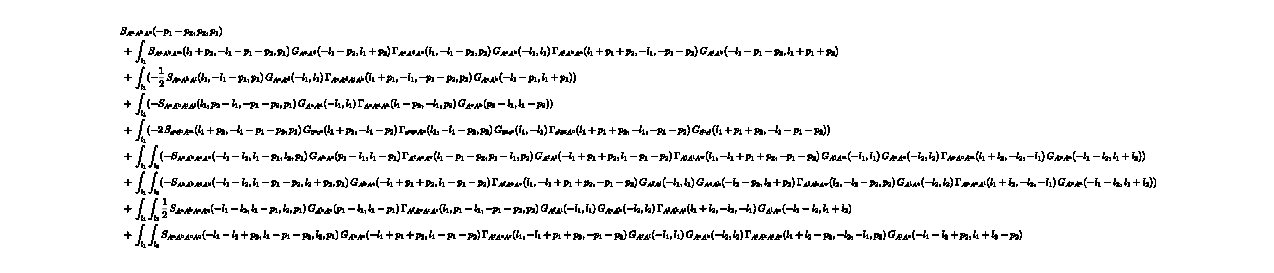

```mathematica
DSEA3=TakeDerivatives[MakeDSE[Setup,A[i1]],{A[i3],A[i2]},"Symmetries"->symmetryP3]//FTruncate//FSimplify[#,"Symmetries"->symmetryP3]&//FPlot//FRoute//FPrint;
DSEA3Result=Map[
(FormTrace[
F[TBGetProjector["AAAClassTrans",1,{i3,i2,i1}/.#["ExternalIndices"]],#["Expression"]/.MakeDiagrammaticRules[]]
,SP3FormRule,SP3FormRule]//dressingRules//(FORMSimplify[#,SP3FormRule,SP3FormRule]&)//SPParam)&,
DSEA3]
```

## 4Point

```mathematica
symmetryP4={Map[Join[#/.Cycles->Sequence,{1}]&,PermutationCycles/@Permutations[{1,2,3,4}]],{i1,i2,i3,i4}};
```

```mathematica
DSEA4=TakeDerivatives[MakeDSE[Setup,A[i1]],{A[i4],A[i3],A[i2]},"Symmetries"->symmetryP4]//FTruncate//FSimplify[#,"Symmetries"->symmetryP4]&//FPlot//FRoute//FPrint;
```

24 -Graphics--36 -Graphics-+18 -Graphics-+72 -Graphics-+36 -Graphics--18 -Graphics--36 -Graphics--36 -Graphics--72 -Graphics--72 -Graphics--72 -Graphics--6 -Graphics-+72 -Graphics-+144 -Graphics-+24 -Graphics-

-Graphics-

## fRG

## 2-Point

```mathematica
symmetryP2={Map[Join[#/.Cycles->Sequence,{1}]&,PermutationCycles/@Permutations[{1,2}]],{i1,i2}};
```


--Graphics-/2-2 -Graphics-+-Graphics-

-Graphics-

(((1+k^6) dtZA[(1+k^6)^(1/6)] RB[k^2,l1^2]+(1+k^6) RBdot[k^2,l1^2] ZA[(1+k^6)^(1/6)]-50 k^6 RB[k^2,l1^2] (ZA[(1+k^6)^(1/6)]-ZA[51/50 (1+k^6)^(1/6)])) ((l1^2-p^2)^2 (2+cos[p,l1]^2) ZA3[√(2/3) √(l1^2+p^2+l1 p cos[p,l1])]^2+(l1^2+p^2+2 l1 p cos[p,l1]) (-7+cos[p,l1]^2) ZA4[(√(l1^2+p^2))/(√2)]))/((1+k^6) l1^4 (l1^2+p^2+2 l1 p cos[p,l1]) Zc[l1]^2)+(12 ((1+k^6) dtZA[(1+k^6)^(1/6)] RB[k^2,l1^2]+(1+k^6) RBdot[k^2,l1^2] ZA[(1+k^6)^(1/6)]-50 k^6 RB[k^2,l1^2] (ZA[(1+k^6)^(1/6)]-ZA[51/50 (1+k^6)^(1/6)])) ZA3[√(2/3) √(l1^2+p^2+l1 p cos[p,l1])]^2)/((1+k^6) (l1^2+p^2+2 l1 p cos[p,l1])^2 Zc[l1]^2 Zc[√(l1^2+p^2+2 l1 p cos[p,l1])])+(4 p cos[p,l1] (6 l1^2-7 l1 p cos[p,l1]-6 p^2 cos[p,l1]^2) ((1+k^6) dtZA[(1+k^6)^(1/6)] RB[k^2,l1^2]+(1+k^6) RBdot[k^2,l1^2] ZA[(1+k^6)^(1/6)]-50 k^6 RB[k^2,l1^2] (ZA[(1+k^6)^(1/6)]-ZA[51/50 (1+k^6)^(1/6)])) ZA3[√(2/3) √(l1^2+p^2+l1 p cos[p,l1])]^2)/((1+k^6) l1^3 (l1^2+p^2+2 l1 p cos[p,l1])^2 Zc[l1]^2 Zc[√(l1^2+p^2+2 l1 p cos[p,l1])])+(4 p^2 (8 l1^2+3 p^2+6 l1 p cos[p,l1]-3 p^2 cos[p,l1]^2) ((1+k^6) dtZA[(1+k^6)^(1/6)] RB[k^2,l1^2]+(1+k^6) RBdot[k^2,l1^2] ZA[(1+k^6)^(1/6)]-50 k^6 RB[k^2,l1^2] (ZA[(1+k^6)^(1/6)]-ZA[51/50 (1+k^6)^(1/6)])) ZA3[√(2/3) √(l1^2+p^2+l1 p cos[p,l1])]^2)/((1+k^6) l1^4 (l1^2+p^2+2 l1 p cos[p,l1])^2 Zc[l1]^2 Zc[√(l1^2+p^2+2 l1 p cos[p,l1])])+(2 (dtZc[k] RB[k^2,l1^2]+RBdot[k^2,l1^2] Zc[k]-50 RB[k^2,l1^2] (Zc[k]-Zc[(51 k)/50])) ZccbA[√(2/3) √(l1^2+p^2-l1 p cos[p,l1])]^2)/(l1^2 (l1^2+p^2-2 l1 p cos[p,l1]) ZA[l1]^2 ZA[√(l1^2+p^2-2 l1 p cos[p,l1])])-1/l1^3 2 cos[p,l1]^2 ((6 l1^3 ((1+k^6) dtZA[(1+k^6)^(1/6)] RB[k^2,l1^2]+(1+k^6) RBdot[k^2,l1^2] ZA[(1+k^6)^(1/6)]-50 k^6 RB[k^2,l1^2] (ZA[(1+k^6)^(1/6)]-ZA[51/50 (1+k^6)^(1/6)])) ZA3[√(2/3) √(l1^2+p^2+l1 p cos[p,l1])]^2)/((1+k^6) (l1^2+p^2+2 l1 p cos[p,l1])^2 Zc[l1]^2 Zc[√(l1^2+p^2+2 l1 p cos[p,l1])])+(2 l1 p cos[p,l1] (6 l1+p cos[p,l1]) ((1+k^6) dtZA[(1+k^6)^(1/6)] RB[k^2,l1^2]+(1+k^6) RBdot[k^2,l1^2] ZA[(1+k^6)^(1/6)]-50 k^6 RB[k^2,l1^2] (ZA[(1+k^6)^(1/6)]-ZA[51/50 (1+k^6)^(1/6)])) ZA3[√(2/3) √(l1^2+p^2+l1 p cos[p,l1])]^2)/((1+k^6) (l1^2+p^2+2 l1 p cos[p,l1])^2 Zc[l1]^2 Zc[√(l1^2+p^2+2 l1 p cos[p,l1])])+(l1 (dtZc[k] RB[k^2,l1^2]+RBdot[k^2,l1^2] Zc[k]-50 RB[k^2,l1^2] (Zc[k]-Zc[(51 k)/50])) ZccbA[√(2/3) √(l1^2+p^2-l1 p cos[p,l1])]^2)/((l1^2+p^2-2 l1 p cos[p,l1]) ZA[l1]^2 ZA[√(l1^2+p^2-2 l1 p cos[p,l1])]))

```mathematica
fRGAA=TakeDerivatives[WetterichEquation,{A[i1],A[i2]}]//FTruncate//FSimplify[#,"Symmetries"->symmetryP2]&//FPlot//FRoute//FPrint;
traceExprAA=F[TBGetProjector["AA",1,{i1,i2}/.fRGAA["1-Loop"]["ExternalIndices"]],(fRGAA["1-Loop"]["Expression"]/.MakeDiagrammaticRules[])];
FlowAA=FormTrace[traceExprAA]//dressingRules//FORMSimplify//PropParam
```

```mathematica
fRGcbc=TakeDerivatives[WetterichEquation,{cb[i1],c[i2]}]//FTruncate//FSimplify//FPlot//FRoute//FPrint;
traceExprcbc=F[TBGetProjector["cbc",1,{i1,i2}/.fRGcbc["1-Loop"]["ExternalIndices"]],(fRGcbc["1-Loop"]["Expression"]/.MakeDiagrammaticRules[])];
Flowcbc=FormTrace[traceExprcbc]//dressingRules//FORMSimplify//PropParam
```

--Graphics---Graphics-

-Graphics-

-((3 p^2 (-1+cos[p,l1]^2) ((1+k^6) RBdot[k^2,l1^2] (-l1^2 ZA[√(l1^2+p^2+2 l1 p cos[p,l1])] Zc[k] Zc[l1]^2+(l1^2+p^2+2 l1 p cos[p,l1]) ZA[(1+k^6)^(1/6)] ZA[l1]^2 Zc[√(l1^2+p^2+2 l1 p cos[p,l1])])-RB[k^2,l1^2] ((1+k^6) l1^2 ZA[√(l1^2+p^2+2 l1 p cos[p,l1])] (dtZc[k]+50 (-Zc[k]+Zc[(51 k)/50])) Zc[l1]^2-(l1^2+p^2+2 l1 p cos[p,l1]) ((1+k^6) dtZA[(1+k^6)^(1/6)]+50 k^6 (-ZA[(1+k^6)^(1/6)]+ZA[51/50 (1+k^6)^(1/6)])) ZA[l1]^2 Zc[√(l1^2+p^2+2 l1 p cos[p,l1])])) ZccbA[√(2/3) √(l1^2+p^2+l1 p cos[p,l1])]^2)/((1+k^6) l1^4 (l1^2+p^2+2 l1 p cos[p,l1])^2 ZA[l1]^2 ZA[√(l1^2+p^2+2 l1 p cos[p,l1])] Zc[l1]^2 Zc[√(l1^2+p^2+2 l1 p cos[p,l1])]))

## 3Point

```mathematica
symmetryP3={Map[Join[#/.Cycles->Sequence,{1}]&,PermutationCycles/@Permutations[{1,2,3}]],{i1,i2,i3}};
SP3FormRule=MakeSPFormRule[{l1},p,{p1,p2,p3}];
```

```mathematica
fRGAcbc=TakeDerivatives[WetterichEquation,{A[i1],cb[i2],c[i3]}]//FTruncate//FSimplify//FPlot//FRoute//FPrint;
projectorAcbc=TBGetProjector["Acbc",1,{i1,i2,i3}/.fRGAcbc["1-Loop"]["ExternalIndices"]];
traceExprAcbc=F[projectorAcbc,(fRGAcbc["1-Loop"]["Expression"]/.MakeDiagrammaticRules[])];FlowAcbc=FormTrace[traceExprAcbc,SP3FormRule,SP3FormRule]//dressingRules//FORMSimplify[#,SP3FormRule,SP3FormRule]&//SPParam
```

--Graphics---Graphics-+-Graphics-+-Graphics-+-Graphics---Graphics-

-Graphics-

(p (cos[p1,l1]+2 cos[p2,l1]) (-l1+p cos[p2,l1]+2 l1 cos[p2,l1]^2+2 cos[p1,l1] (p+l1 cos[p2,l1])) (dtZc[k] RB[k^2,l1^2]+RBdot[k^2,l1^2] Zc[k]-50 RB[k^2,l1^2] (Zc[k]-Zc[(51 k)/50])) ZccbA[√(2/3) √(l1^2+p^2-l1 p cos[p1,l1])] ZccbA[√(2/3) √(l1^2+p^2+l1 p cos[p2,l1])] ZccbA[√((2 l1^2)/3+p^2+2/3 l1 p (-cos[p1,l1]+cos[p2,l1]))])/(2 l1^2 (l1^2+p^2-2 l1 p cos[p1,l1]) (l1^2+p^2+2 l1 p cos[p2,l1])^2 ZA[l1]^2 ZA[√(l1^2+p^2-2 l1 p cos[p1,l1])] Zc[√(l1^2+p^2+2 l1 p cos[p2,l1])])+(p (cos[p1,l1]+2 cos[p2,l1]) (-l1+p cos[p2,l1]+2 l1 cos[p2,l1]^2-cos[p1,l1] (p-2 l1 cos[p2,l1])) (dtZc[k] RB[k^2,l1^2]+RBdot[k^2,l1^2] Zc[k]-50 RB[k^2,l1^2] (Zc[k]-Zc[(51 k)/50])) ZccbA[√(2/3) √(l1^2+p^2+l1 p cos[p1,l1])] ZccbA[√(2/3) √(l1^2+p^2+l1 p (cos[p1,l1]+cos[p2,l1]))] ZccbA[√((2 l1^2)/3+p^2+2/3 l1 p (2 cos[p1,l1]+cos[p2,l1]))])/(2 l1^2 (l1^2+p^2+2 l1 p cos[p1,l1]) (l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))^2 ZA[l1]^2 ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])] Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))])+(p ZA3[√(2/3) √(l1^2+p^2+l1 p cos[p1,l1])] (-1/((l1^2+p^2-2 l1 p cos[p2,l1]) ZA[√(l1^2+p^2-2 l1 p cos[p2,l1])])(-3 p (2 l1^2+p^2)+2 l1 (-2 l1^2+p^2) cos[p2,l1]+4 l1^2 p cos[p1,l1]^3 cos[p2,l1]+4 l1^2 p cos[p2,l1]^2+8 (l1^2)^(3/2) cos[p2,l1]^3+2 l1 cos[p1,l1]^2 (l1 p+(2 l1^2-5 p^2) cos[p2,l1]+6 l1 p cos[p2,l1]^2)+cos[p1,l1] (-6 (p^2)^(3/2) cos[p2,l1]+l1 p^2 (-5+4 cos[p2,l1]^2)+2 l1^2 p cos[p2,l1] (-3+4 cos[p2,l1]^2)+2 (l1^2)^(3/2) (-1+6 cos[p2,l1]^2))) ((1+k^6) dtZA[(1+k^6)^(1/6)] RB[k^2,l1^2]+(1+k^6) RBdot[k^2,l1^2] ZA[(1+k^6)^(1/6)]-50 k^6 RB[k^2,l1^2] (ZA[(1+k^6)^(1/6)]-ZA[51/50 (1+k^6)^(1/6)])) ZccbA[√((2 l1^2)/3+p^2+2/3 l1 p (cos[p1,l1]-cos[p2,l1]))] ZccbA[√(2/3) √(l1^2+p^2-l1 p cos[p2,l1])]-(((l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1])) (-3 p (2 l1^2+p^2)+2 l1 (2 l1^2-p^2) cos[p2,l1]+4 l1^2 p cos[p2,l1]^2-8 (l1^2)^(3/2) cos[p2,l1]^3+2 l1 p cos[p1,l1]^3 (7 p-2 l1 cos[p2,l1])+2 cos[p1,l1]^2 (3 p (2 l1^2+p^2)+(-2 l1^3+9 l1 p^2) cos[p2,l1]-6 l1^2 p cos[p2,l1]^2)+cos[p1,l1] (6 (p^2)^(3/2) cos[p2,l1]+(l1^2)^(3/2) (2-12 cos[p2,l1]^2)+2 l1^2 p cos[p2,l1] (7-4 cos[p2,l1]^2)+l1 p^2 (-7+4 cos[p2,l1]^2))) ((1+k^6) dtZA[(1+k^6)^(1/6)] RB[k^2,l1^2]+(1+k^6) RBdot[k^2,l1^2] ZA[(1+k^6)^(1/6)]-50 k^6 RB[k^2,l1^2] (ZA[(1+k^6)^(1/6)]-ZA[51/50 (1+k^6)^(1/6)])) ZA[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+(1+k^6) l1^2 (3 p (2 l1^2+p^2)+2 l1 (-2 l1^2+p^2) cos[p2,l1]-4 l1^2 p cos[p2,l1]^2+8 (l1^2)^(3/2) cos[p2,l1]^3+2 l1 p cos[p1,l1]^3 (-7 p+2 l1 cos[p2,l1])+2 cos[p1,l1]^2 (-3 (2 l1^2 p+p^3)+(2 l1^3-9 l1 p^2) cos[p2,l1]+6 l1^2 p cos[p2,l1]^2)+cos[p1,l1] (-6 (p^2)^(3/2) cos[p2,l1]+l1 p^2 (7-4 cos[p2,l1]^2)+2 l1^2 p cos[p2,l1] (-7+4 cos[p2,l1]^2)+2 (l1^2)^(3/2) (-1+6 cos[p2,l1]^2))) (dtZc[k] RB[k^2,l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1])]+RBdot[k^2,l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1])] Zc[k]-50 RB[k^2,l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1])] (Zc[k]-Zc[(51 k)/50])) Zc[l1]) ZccbA[√(2/3) √(l1^2+p^2+l1 p (cos[p1,l1]+cos[p2,l1]))] ZccbA[√((2 l1^2)/3+p^2+2/3 l1 p (2 cos[p1,l1]+cos[p2,l1]))])/((l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))^2 ZA[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]^2)))/(2 (1+k^6) l1^4 (l1^2+p^2+2 l1 p cos[p1,l1])^2 Zc[l1]^2 Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])])-(p (-3 p+2 l1 cos[p1,l1]+4 l1 cos[p2,l1]) (-1+2 cos[p1,l1] cos[p2,l1]+2 cos[p2,l1]^2) ((1+k^6) dtZA[(1+k^6)^(1/6)] RB[k^2,l1^2]+(1+k^6) RBdot[k^2,l1^2] ZA[(1+k^6)^(1/6)]-50 k^6 RB[k^2,l1^2] (ZA[(1+k^6)^(1/6)]-ZA[51/50 (1+k^6)^(1/6)])) ZccbA[√(2/3) √(l1^2+p^2-l1 p cos[p2,l1])] ZccbA[√(2/3) √(l1^2+p^2-l1 p (cos[p1,l1]+cos[p2,l1]))] ZccbA[√((2 l1^2)/3+p^2-2/3 l1 p (cos[p1,l1]+2 cos[p2,l1]))])/(4 (1+k^6) l1^4 (l1^2+p^2-2 l1 p cos[p2,l1]) (l1^2+p^2-2 l1 p (cos[p1,l1]+cos[p2,l1])) ZA[√(l1^2+p^2-2 l1 p cos[p2,l1])] ZA[√(l1^2+p^2-2 l1 p (cos[p1,l1]+cos[p2,l1]))] Zc[l1]^2)

```mathematica
fRGA3=TakeDerivatives[WetterichEquation,{A[i1],A[i2],A[i3]}]//FTruncate//FSimplify[#,"Symmetries"->symmetryP3]&//FPlot//FRoute//FPrint;
projectorA3=TBGetProjector["AAAClassTrans",1,{i1,i2,i3}/.fRGA3["1-Loop"]["ExternalIndices"]]//TBProjectToSymmetricPoint[#,l1,p,p1,p2,p3]&//Simplify;
traceExprA3=F[projectorA3,(fRGA3["1-Loop"]["Expression"]/.MakeDiagrammaticRules[])];
FlowA3=FormTrace[traceExprA3,{},SP3FormRule]//dressingRules//FORMSimplify[#,{},SP3FormRule]&//SPParam
```

3 -Graphics--6 -Graphics--3 -Graphics-

-Graphics-

-((((1+k^6) dtZA[(1+k^6)^(1/6)] RB[k^2,l1^2]+(1+k^6) RBdot[k^2,l1^2] ZA[(1+k^6)^(1/6)]-50 k^6 RB[k^2,l1^2] (ZA[(1+k^6)^(1/6)]-ZA[51/50 (1+k^6)^(1/6)])) ZA3[√(2/3) √(l1^2+p^2+l1 p cos[p1,l1])] (-32 (l1^2)^(3/2) p^2 cos[p2,l1]^5 ZA3[√(2/3) √(l1^2+p^2+l1 p (cos[p1,l1]+cos[p2,l1]))] ZA3[√((2 l1^2)/3+p^2+2/3 l1 p (2 cos[p1,l1]+cos[p2,l1]))] (-2 l1^2+(l1^4-p^4) Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])])+64 l1^4 (p^2)^(3/2) cos[p1,l1]^6 ZA3[√(2/3) √(l1^2+p^2+l1 p (cos[p1,l1]+cos[p2,l1]))] ZA3[√((2 l1^2)/3+p^2+2/3 l1 p (2 cos[p1,l1]+cos[p2,l1]))] (-2+(l1^2-p^2) Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])]+(l1^2-p^2) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))])-16 l1^2 p cos[p2,l1]^4 (6 p^2 ZA4[1/2 √(2 l1^2+3 p^2+2 l1 p cos[p1,l1])] (2 l1^2+(-l1^4+p^4) Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])]) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+ZA3[√(2/3) √(l1^2+p^2+l1 p (cos[p1,l1]+cos[p2,l1]))] ZA3[√((2 l1^2)/3+p^2+2/3 l1 p (2 cos[p1,l1]+cos[p2,l1]))] (-24 l1^4-60 l1^2 p^2+2 l1^6 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]-2 l1^4 p^2 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+(l1^4-p^4) Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])] (3 (l1^2+7 p^2)+p^2 (l1^2-p^2) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))])))+16 (l1^2)^(3/2) p^2 cos[p1,l1]^5 (3 p^2 ZA4[1/2 √(2 l1^2+3 p^2+2 l1 p cos[p1,l1])] (53+13 (l1^2-p^2) Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])]) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+ZA3[√(2/3) √(l1^2+p^2+l1 p (cos[p1,l1]+cos[p2,l1]))] ZA3[√((2 l1^2)/3+p^2+2/3 l1 p (2 cos[p1,l1]+cos[p2,l1]))] (-52 l1^2-112 p^2+8 l1^4 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]-17 l1^2 p^2 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+9 p^4 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+(l1^2-p^2) Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])] (8 l1^2-9 p^2+2 p^2 (l1^2-p^2) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))])+2 p cos[p2,l1] (-12 l1+7 ((l1^2)^(3/2)-l1 p^2) Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])]+5 ((l1^2)^(3/2)-l1 p^2) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))])))-8 l1 cos[p2,l1]^3 (-12 p^2 (l1^2+p^2) ZA4[1/2 √(2 l1^2+3 p^2+2 l1 p cos[p1,l1])] (-2 l1^2+(l1^4-p^4) Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])]) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+ZA3[√(2/3) √(l1^2+p^2+l1 p (cos[p1,l1]+cos[p2,l1]))] ZA3[√((2 l1^2)/3+p^2+2/3 l1 p (2 cos[p1,l1]+cos[p2,l1]))] ((l1^4-p^4) Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])] (2 (l1^4+15 l1^2 p^2+11 p^4)+l1^2 p^2 (l1^2-p^2) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))])+2 l1^2 (-2 (6 l1^4+25 l1^2 p^2+16 p^4)+(l1^6-l1^4 p^2) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))])))+3 p (6 (l1^2+p^2)^2 ZA4[1/2 √(2 l1^2+3 p^2+2 l1 p cos[p1,l1])] (-36 l1^2-22 p^2+7 (l1^4-p^4) Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])]) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+ZA3[√(2/3) √(l1^2+p^2+l1 p (cos[p1,l1]+cos[p2,l1]))] ZA3[√((2 l1^2)/3+p^2+2/3 l1 p (2 cos[p1,l1]+cos[p2,l1]))] (96 l1^6+496 l1^4 p^2+504 l1^2 p^4+132 p^6+(36 l1^8+22 l1^6 p^2-36 l1^4 p^4-22 l1^2 p^6) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+(l1^4-p^4) Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])] (36 l1^4+22 l1^2 p^2+7 p^2 (l1^4-p^4) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))])))+2 l1 cos[p2,l1] (36 p^2 (l1^2+p^2) ZA4[1/2 √(2 l1^2+3 p^2+2 l1 p cos[p1,l1])] (-36 l1^2-22 p^2+7 (l1^4-p^4) Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])]) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+ZA3[√(2/3) √(l1^2+p^2+l1 p (cos[p1,l1]+cos[p2,l1]))] ZA3[√((2 l1^2)/3+p^2+2/3 l1 p (2 cos[p1,l1]+cos[p2,l1]))] (288 l1^4 p^2+964 l1^2 p^4+462 p^6-44 l1^8 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+42 l1^6 p^2 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+2 l1^4 p^4 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+(l1^4-p^4) Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])] (22 l1^4+195 l1^2 p^2+66 p^4+(11 l1^4 p^2+21 l1^2 p^4-32 p^6) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))])))+4 p cos[p2,l1]^2 (6 ZA4[1/2 √(2 l1^2+3 p^2+2 l1 p cos[p1,l1])] (-2 (l1^6+56 l1^4 p^2+34 l1^2 p^4)+(l1^8+23 l1^6 p^2-23 l1^2 p^6-p^8) Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])]) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+ZA3[√(2/3) √(l1^2+p^2+l1 p (cos[p1,l1]+cos[p2,l1]))] ZA3[√((2 l1^2)/3+p^2+2/3 l1 p (2 cos[p1,l1]+cos[p2,l1]))] (-24 l1^6-56 l1^4 p^2+72 l1^2 p^4-42 l1^8 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]-22 l1^6 p^2 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+64 l1^4 p^4 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+(l1^4-p^4) Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])] (13 (l1^4+5 l1^2 p^2)+(12 l1^4 p^2-11 l1^2 p^4-p^6) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))])))+8 l1^2 p cos[p1,l1]^4 (2 l1^6 ZA3[√(2/3) √(l1^2+p^2+l1 p (cos[p1,l1]+cos[p2,l1]))] ZA3[√((2 l1^2)/3+p^2+2/3 l1 p (2 cos[p1,l1]+cos[p2,l1]))] (5 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])] (5+2 p^2 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]))+2 (l1^2)^(5/2) p cos[p2,l1] ZA3[√(2/3) √(l1^2+p^2+l1 p (cos[p1,l1]+cos[p2,l1]))] ZA3[√((2 l1^2)/3+p^2+2/3 l1 p (2 cos[p1,l1]+cos[p2,l1]))] (18 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])] (22+5 p^2 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]))+2 l1 (p^2)^(3/2) cos[p2,l1] (18 ZA4[1/2 √(2 l1^2+3 p^2+2 l1 p cos[p1,l1])] (17-5 p^2 Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])]) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+5 ZA3[√(2/3) √(l1^2+p^2+l1 p (cos[p1,l1]+cos[p2,l1]))] ZA3[√((2 l1^2)/3+p^2+2/3 l1 p (2 cos[p1,l1]+cos[p2,l1]))] (-56-5 p^2 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+p^2 Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])] (14+p^2 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))])))+3 p^4 (ZA4[1/2 √(2 l1^2+3 p^2+2 l1 p cos[p1,l1])] (172-39 p^2 Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])]) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+ZA3[√(2/3) √(l1^2+p^2+l1 p (cos[p1,l1]+cos[p2,l1]))] ZA3[√((2 l1^2)/3+p^2+2/3 l1 p (2 cos[p1,l1]+cos[p2,l1]))] (11 (-19+p^2 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))])+p^2 Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])] (11+5 p^2 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))])))-2 (l1^2)^(3/2) p cos[p2,l1] (-90 p^2 ZA4[1/2 √(2 l1^2+3 p^2+2 l1 p cos[p1,l1])] Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])] Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+ZA3[√(2/3) √(l1^2+p^2+l1 p (cos[p1,l1]+cos[p2,l1]))] ZA3[√((2 l1^2)/3+p^2+2/3 l1 p (2 cos[p1,l1]+cos[p2,l1]))] (130-7 p^2 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+2 p^2 Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])] (46+5 p^2 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))])))+l1^4 (315 p^2 ZA4[1/2 √(2 l1^2+3 p^2+2 l1 p cos[p1,l1])] Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])] Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+ZA3[√(2/3) √(l1^2+p^2+l1 p (cos[p1,l1]+cos[p2,l1]))] ZA3[√((2 l1^2)/3+p^2+2/3 l1 p (2 cos[p1,l1]+cos[p2,l1]))] (p^2 Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])] (-114+20 cos[p2,l1]^2+7 p^2 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))])-6 (16+19 p^2 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))])))-l1^2 p^2 (6 ZA4[1/2 √(2 l1^2+3 p^2+2 l1 p cos[p1,l1])] (-106+33 p^2 Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])]) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+ZA3[√(2/3) √(l1^2+p^2+l1 p (cos[p1,l1]+cos[p2,l1]))] ZA3[√((2 l1^2)/3+p^2+2/3 l1 p (2 cos[p1,l1]+cos[p2,l1]))] (622+20 cos[p2,l1]^2 (1+p^2 Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])])-71 p^2 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+p^2 Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])] (-71+26 p^2 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]))))+4 cos[p1,l1]^3 (2 (l1^2)^(9/2) ZA3[√(2/3) √(l1^2+p^2+l1 p (cos[p1,l1]+cos[p2,l1]))] ZA3[√((2 l1^2)/3+p^2+2/3 l1 p (2 cos[p1,l1]+cos[p2,l1]))] (2 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])] (2+p^2 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]))+2 l1^8 p cos[p2,l1] ZA3[√(2/3) √(l1^2+p^2+l1 p (cos[p1,l1]+cos[p2,l1]))] ZA3[√((2 l1^2)/3+p^2+2/3 l1 p (2 cos[p1,l1]+cos[p2,l1]))] (19 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])] (21+8 p^2 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]))-2 l1^6 p cos[p2,l1] (-588 p^2 ZA4[1/2 √(2 l1^2+3 p^2+2 l1 p cos[p1,l1])] Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])] Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+ZA3[√(2/3) √(l1^2+p^2+l1 p (cos[p1,l1]+cos[p2,l1]))] ZA3[√((2 l1^2)/3+p^2+2/3 l1 p (2 cos[p1,l1]+cos[p2,l1]))] (192+p^2 (109+20 cos[p2,l1]^2) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+p^2 Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])] (347+20 cos[p2,l1]^2-14 p^2 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))])))+6 l1^2 (p^2)^(5/2) cos[p2,l1] (2 ZA4[1/2 √(2 l1^2+3 p^2+2 l1 p cos[p1,l1])] (115-32 p^2 Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])]) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+ZA3[√(2/3) √(l1^2+p^2+l1 p (cos[p1,l1]+cos[p2,l1]))] ZA3[√((2 l1^2)/3+p^2+2/3 l1 p (2 cos[p1,l1]+cos[p2,l1]))] (-11 (38+p^2 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))])+5 p^2 Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])] (11+2 p^2 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))])))+l1 p^6 (3 ZA4[1/2 √(2 l1^2+3 p^2+2 l1 p cos[p1,l1])] (185-39 p^2 Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])]) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+2 ZA3[√(2/3) √(l1^2+p^2+l1 p (cos[p1,l1]+cos[p2,l1]))] ZA3[√((2 l1^2)/3+p^2+2/3 l1 p (2 cos[p1,l1]+cos[p2,l1]))] (11 (-42+p^2 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))])+p^2 Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])] (11+12 p^2 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))])))+(l1^2)^(3/2) p^4 (3 ZA4[1/2 √(2 l1^2+3 p^2+2 l1 p cos[p1,l1])] (234-321 p^2 Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])]-4 cos[p2,l1]^2 (-41+25 p^2 Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])])) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+ZA3[√(2/3) √(l1^2+p^2+l1 p (cos[p1,l1]+cos[p2,l1]))] ZA3[√((2 l1^2)/3+p^2+2/3 l1 p (2 cos[p1,l1]+cos[p2,l1]))] (-1920+79 p^2 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+8 cos[p2,l1]^2 (-68+79 p^2 Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])]-16 p^2 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))])+p^2 Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])] (79+22 p^2 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))])))+(l1^2)^(7/2) (711 p^2 ZA4[1/2 √(2 l1^2+3 p^2+2 l1 p cos[p1,l1])] Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])] Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+ZA3[√(2/3) √(l1^2+p^2+l1 p (cos[p1,l1]+cos[p2,l1]))] ZA3[√((2 l1^2)/3+p^2+2/3 l1 p (2 cos[p1,l1]+cos[p2,l1]))] (-48-3 p^2 (77+4 cos[p2,l1]^2) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+p^2 Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])] (-231+20 cos[p2,l1]^2+66 p^2 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))])))+2 l1^4 (p^2)^(3/2) cos[p2,l1] (6 ZA4[1/2 √(2 l1^2+3 p^2+2 l1 p cos[p1,l1])] (151-66 p^2 Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])]) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+ZA3[√(2/3) √(l1^2+p^2+l1 p (cos[p1,l1]+cos[p2,l1]))] ZA3[√((2 l1^2)/3+p^2+2/3 l1 p (2 cos[p1,l1]+cos[p2,l1]))] (-1244+123 p^2 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+20 cos[p2,l1]^2 (2+p^2 Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])]+p^2 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))])+Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])] (161 p^2-52 p^4 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))])))+(l1^2)^(5/2) p^2 (3 ZA4[1/2 √(2 l1^2+3 p^2+2 l1 p cos[p1,l1])] (265+p^2 (123+100 cos[p2,l1]^2) Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])]) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]-2 ZA3[√(2/3) √(l1^2+p^2+l1 p (cos[p1,l1]+cos[p2,l1]))] ZA3[√((2 l1^2)/3+p^2+2/3 l1 p (2 cos[p1,l1]+cos[p2,l1]))] (388-63 p^2 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+cos[p2,l1]^2 (8+326 p^2 Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])]-70 p^2 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))])+Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])] (-63 p^2+57 p^4 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]))))-2 cos[p1,l1] (-32 l1^4 (p^2)^(3/2) cos[p2,l1]^5 ZA3[√(2/3) √(l1^2+p^2+l1 p (cos[p1,l1]+cos[p2,l1]))] ZA3[√((2 l1^2)/3+p^2+2/3 l1 p (2 cos[p1,l1]+cos[p2,l1]))] (1+(-l1^2+p^2) Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])])-9 l1 (l1^2+p^2) ZA4[1/2 √(2 l1^2+3 p^2+2 l1 p cos[p1,l1])] (-4 (45 l1^2 p^2+31 p^4)+(11 l1^6+53 l1^4 p^2-11 l1^2 p^4-53 p^6) Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])]) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]-l1 ZA3[√(2/3) √(l1^2+p^2+l1 p (cos[p1,l1]+cos[p2,l1]))] ZA3[√((2 l1^2)/3+p^2+2/3 l1 p (2 cos[p1,l1]+cos[p2,l1]))] (576 l1^4 p^2+1928 l1^2 p^4+924 p^6+(-22 l1^8+237 l1^6 p^2+46 l1^4 p^4-195 l1^2 p^6-66 p^8) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+(l1^2-p^2) Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])] (-22 l1^6+215 l1^4 p^2+261 l1^2 p^4+66 p^6+(22 l1^6 p^2+64 l1^4 p^4-22 l1^2 p^6-64 p^8) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]))+8 (l1^2)^(3/2) p^2 cos[p2,l1]^4 (12 p^2 ZA4[1/2 √(2 l1^2+3 p^2+2 l1 p cos[p1,l1])] (1+(-l1^2+p^2) Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])]) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+ZA3[√(2/3) √(l1^2+p^2+l1 p (cos[p1,l1]+cos[p2,l1]))] ZA3[√((2 l1^2)/3+p^2+2/3 l1 p (2 cos[p1,l1]+cos[p2,l1]))] (-58 l1^2-44 p^2+6 (l1^4-l1^2 p^2) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+(l1^2-p^2) Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])] (13 l1^2+49 p^2+2 p^2 (l1^2-p^2) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))])))+4 l1^2 p cos[p2,l1]^3 (12 p^2 ZA4[1/2 √(2 l1^2+3 p^2+2 l1 p cos[p1,l1])] (2 (4 l1^2+p^2)-5 (l1^4-p^4) Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])]) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+ZA3[√(2/3) √(l1^2+p^2+l1 p (cos[p1,l1]+cos[p2,l1]))] ZA3[√((2 l1^2)/3+p^2+2/3 l1 p (2 cos[p1,l1]+cos[p2,l1]))] (4 (-42 l1^4-101 l1^2 p^2+6 p^4+4 (l1^6-l1^4 p^2) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))])+(l1^2-p^2) Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])] (19 l1^4+214 l1^2 p^2+183 p^4+(7 l1^4 p^2-2 l1^2 p^4-5 p^6) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))])))+p cos[p2,l1] (12 ZA4[1/2 √(2 l1^2+3 p^2+2 l1 p cos[p1,l1])] (2 l1^2 (l1^4+164 l1^2 p^2+121 p^4)+(-34 l1^8-119 l1^6 p^2+33 l1^4 p^4+119 l1^2 p^6+p^8) Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])]) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+ZA3[√(2/3) √(l1^2+p^2+l1 p (cos[p1,l1]+cos[p2,l1]))] ZA3[√((2 l1^2)/3+p^2+2/3 l1 p (2 cos[p1,l1]+cos[p2,l1]))] (264 l1^6+652 l1^4 p^2+306 l1^2 p^4+396 p^6+2 (143 l1^8-74 l1^6 p^2-80 l1^4 p^4+11 l1^2 p^6) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]-(l1^2-p^2) Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])] (-66 l1^6+430 l1^4 p^2+282 l1^2 p^4+(99 l1^6 p^2+53 l1^4 p^4-141 l1^2 p^6-11 p^8) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))])))+2 l1 cos[p2,l1]^2 (6 p^2 ZA4[1/2 √(2 l1^2+3 p^2+2 l1 p cos[p1,l1])] (2 (9 l1^4+64 l1^2 p^2+p^4)+(-43 l1^6-52 l1^4 p^2+85 l1^2 p^4+10 p^6) Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])]) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+ZA3[√(2/3) √(l1^2+p^2+l1 p (cos[p1,l1]+cos[p2,l1]))] ZA3[√((2 l1^2)/3+p^2+2/3 l1 p (2 cos[p1,l1]+cos[p2,l1]))] (2 (-36 l1^6-6 l1^4 p^2+352 l1^2 p^4+231 p^6+(3 l1^8+72 l1^6 p^2-23 l1^4 p^4-52 l1^2 p^6) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))])+(l1^2-p^2) Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])] (6 l1^6+205 l1^4 p^2+205 l1^2 p^4+110 p^6+(3 l1^6 p^2-34 l1^4 p^4+19 l1^2 p^6+12 p^8) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]))))-2 cos[p1,l1]^2 (16 l1^4 (p^2)^(3/2) cos[p2,l1]^4 ZA3[√(2/3) √(l1^2+p^2+l1 p (cos[p1,l1]+cos[p2,l1]))] ZA3[√((2 l1^2)/3+p^2+2/3 l1 p (2 cos[p1,l1]+cos[p2,l1]))] (-9+7 (l1^2-p^2) Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])]+2 (l1^2-p^2) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))])+8 (l1^2)^(3/2) p^2 cos[p2,l1]^3 (36 p^2 ZA4[1/2 √(2 l1^2+3 p^2+2 l1 p cos[p1,l1])] (1+(-l1^2+p^2) Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])]) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+ZA3[√(2/3) √(l1^2+p^2+l1 p (cos[p1,l1]+cos[p2,l1]))] ZA3[√((2 l1^2)/3+p^2+2/3 l1 p (2 cos[p1,l1]+cos[p2,l1]))] (-4 (31 l1^2+19 p^2)+17 (l1^4-l1^2 p^2) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+(l1^2-p^2) Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])] (4 (5 l1^2+36 p^2)+5 p^2 (l1^2-p^2) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))])))+p (-3 ZA4[1/2 √(2 l1^2+3 p^2+2 l1 p cos[p1,l1])] (106 l1^6-586 l1^4 p^2-458 l1^2 p^4+66 p^6+(211 l1^8+476 l1^6 p^2-198 l1^4 p^4-476 l1^2 p^6-13 p^8) Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])]) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+ZA3[√(2/3) √(l1^2+p^2+l1 p (cos[p1,l1]+cos[p2,l1]))] ZA3[√((2 l1^2)/3+p^2+2/3 l1 p (2 cos[p1,l1]+cos[p2,l1]))] (264 l1^6+652 l1^4 p^2+306 l1^2 p^4+396 p^6+2 (88 l1^8-161 l1^6 p^2-3 l1^4 p^4+76 l1^2 p^6) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]-(l1^2-p^2) Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])] (2 l1^2 (-88 l1^4+73 l1^2 p^2+76 p^4)+(99 l1^6 p^2+53 l1^4 p^4-141 l1^2 p^6-11 p^8) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))])))-2 l1 cos[p2,l1] (3 l1^8 ZA3[√(2/3) √(l1^2+p^2+l1 p (cos[p1,l1]+cos[p2,l1]))] ZA3[√((2 l1^2)/3+p^2+2/3 l1 p (2 cos[p1,l1]+cos[p2,l1]))] (2 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])] (2+p^2 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]))+l1^6 (906 p^2 ZA4[1/2 √(2 l1^2+3 p^2+2 l1 p cos[p1,l1])] Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])] Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+ZA3[√(2/3) √(l1^2+p^2+l1 p (cos[p1,l1]+cos[p2,l1]))] ZA3[√((2 l1^2)/3+p^2+2/3 l1 p (2 cos[p1,l1]+cos[p2,l1]))] (-72-319 p^2 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+11 p^2 Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])] (-34+9 p^2 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))])))+2 p^6 (3 ZA4[1/2 √(2 l1^2+3 p^2+2 l1 p cos[p1,l1])] (64-19 p^2 Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])]) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+ZA3[√(2/3) √(l1^2+p^2+l1 p (cos[p1,l1]+cos[p2,l1]))] ZA3[√((2 l1^2)/3+p^2+2/3 l1 p (2 cos[p1,l1]+cos[p2,l1]))] (-11 (63+p^2 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))])+2 p^2 Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])] (22+9 p^2 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))])))+3 l1^2 p^4 (-2 ZA4[1/2 √(2 l1^2+3 p^2+2 l1 p cos[p1,l1])] (56+235 p^2 Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])]) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+ZA3[√(2/3) √(l1^2+p^2+l1 p (cos[p1,l1]+cos[p2,l1]))] ZA3[√((2 l1^2)/3+p^2+2/3 l1 p (2 cos[p1,l1]+cos[p2,l1]))] (-960+41 p^2 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+p^2 Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])] (38+11 p^2 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))])))+l1^4 p^2 (6 ZA4[1/2 √(2 l1^2+3 p^2+2 l1 p cos[p1,l1])] (96+103 p^2 Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])]) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+ZA3[√(2/3) √(l1^2+p^2+l1 p (cos[p1,l1]+cos[p2,l1]))] ZA3[√((2 l1^2)/3+p^2+2/3 l1 p (2 cos[p1,l1]+cos[p2,l1]))] (4 (-291+53 p^2 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))])+Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])] (166 p^2-171 p^4 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]))))+4 l1^2 p cos[p2,l1]^2 (3 l1^6 ZA3[√(2/3) √(l1^2+p^2+l1 p (cos[p1,l1]+cos[p2,l1]))] ZA3[√((2 l1^2)/3+p^2+2/3 l1 p (2 cos[p1,l1]+cos[p2,l1]))] (3 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])] (2+p^2 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]))+l1^2 p^2 (198 ZA4[1/2 √(2 l1^2+3 p^2+2 l1 p cos[p1,l1])] (-1+p^2 Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])]) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+ZA3[√(2/3) √(l1^2+p^2+l1 p (cos[p1,l1]+cos[p2,l1]))] ZA3[√((2 l1^2)/3+p^2+2/3 l1 p (2 cos[p1,l1]+cos[p2,l1]))] (218-58 p^2 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+23 p^2 Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])] (-5+p^2 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))])))+p^4 (3 ZA4[1/2 √(2 l1^2+3 p^2+2 l1 p cos[p1,l1])] (-50+41 p^2 Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])]) Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+ZA3[√(2/3) √(l1^2+p^2+l1 p (cos[p1,l1]+cos[p2,l1]))] ZA3[√((2 l1^2)/3+p^2+2/3 l1 p (2 cos[p1,l1]+cos[p2,l1]))] (651+24 p^2 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]-p^2 Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])] (273+10 p^2 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))])))+l1^4 (-321 p^2 ZA4[1/2 √(2 l1^2+3 p^2+2 l1 p cos[p1,l1])] Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])] Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+ZA3[√(2/3) √(l1^2+p^2+l1 p (cos[p1,l1]+cos[p2,l1]))] ZA3[√((2 l1^2)/3+p^2+2/3 l1 p (2 cos[p1,l1]+cos[p2,l1]))] (-72+25 p^2 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]+Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])] (382 p^2-16 p^4 Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))])))))))/(44 (1+k^6) l1^4 √(p^2) (l1^2+p^2+2 l1 p cos[p1,l1])^2 (l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))^2 Zc[l1]^2 Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])] Zc[√(l1^2+p^2+2 l1 p (cos[p1,l1]+cos[p2,l1]))]))+((6 p+4 l1 cos[p1,l1]^3-2 p cos[p2,l1]^2-4 l1 cos[p2,l1]^3+cos[p1,l1]^2 (-11 p+6 l1 cos[p2,l1])-cos[p1,l1] cos[p2,l1] (11 p+6 l1 cos[p2,l1])) (dtZc[k] RB[k^2,l1^2]+RBdot[k^2,l1^2] Zc[k]-50 RB[k^2,l1^2] (Zc[k]-Zc[(51 k)/50])) ZccbA[√(2/3) √(l1^2+p^2-l1 p cos[p1,l1])] ZccbA[√(2/3) √(l1^2+p^2-l1 p (cos[p1,l1]+cos[p2,l1]))] ZccbA[√((2 l1^2)/3+p^2-2/3 l1 p (2 cos[p1,l1]+cos[p2,l1]))])/(11 l1^2 √(p^2) (l1^2+p^2-2 l1 p cos[p1,l1]) (l1^2+p^2-2 l1 p (cos[p1,l1]+cos[p2,l1])) ZA[l1]^2 ZA[√(l1^2+p^2-2 l1 p cos[p1,l1])] ZA[√(l1^2+p^2-2 l1 p (cos[p1,l1]+cos[p2,l1]))])

## 4Point

```mathematica
symmetryP4={Map[Join[#/.Cycles->Sequence,{1}]&,PermutationCycles/@Permutations[{1,2,3,4}]],{i1,i2,i3,i4}};
SP4FormRule=MakeSPFormRule[l1,p,p1,p2,p3,p4];
```

```mathematica
fRGA4=TakeDerivatives[WetterichEquation,{A[i1],A[i2],A[i3],A[i4]}]//FTruncate//FSimplify[#,"Symmetries"->symmetryP4]&//FPlot//FRoute//FPrint;
projectorA4=TBGetProjector["AAAAClassTrans",1,{i1,i2,i3,i4}/.fRGA4["1-Loop"]["ExternalIndices"]]//TBProjectToSymmetricPoint[#,l1,p,p1,p2,p3,p4]&//Simplify;
traceExprA4=F[projectorA4,(fRGA4["1-Loop"]["Expression"]/.MakeDiagrammaticRules[])];
FlowA4=FormTrace[traceExprA4,SP4FormRule,SP4FormRule]//.dressingRules//FORMSimplify[#,SP4FormRule,SP4FormRule]&//SPParam
```

3 -Graphics--12 -Graphics--6 -Graphics--24 -Graphics-+12 -Graphics-

-Graphics-